```mathematica
SetDirectory["/Users/Mukesh/Documents/Research/RSD"]
```

/Users/Mukesh/Documents/Research/RSD

```mathematica
da=ReadList["hydra_matterpower_z0.dat",{Number,Number}];
kCAMB=Flatten[Drop[da,{},{2,2}]];
PkCAMB=Flatten[Drop[da,{},{1,1}]];
PlinHydra=Interpolation[da];
```

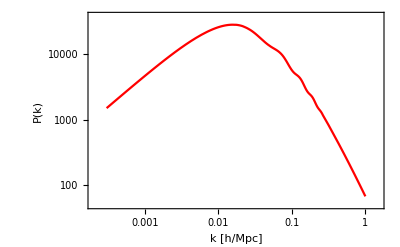

```mathematica
LogLogPlot[PlinHydra[k],{k,0.0003,1},Frame->True,PlotStyle->Red,LabelStyle->{Italic,FontFamily->"Helvetica"},FrameLabel->{"k [h/Mpc]","P(k)"},ColorFunctionScaling->False,ImageSize->400,FrameTicksStyle->20,FrameStyle->21]
```

```mathematica
xs = ReadList["xs.dat", {Number,Number,Number}]
```

{{1,86,99},{1,86,100},{1,86,101},{1,87,95},{1,87,96},{1,87,97},{1,87,98},{1,87,99},{1,87,100},{1,87,101},{1,87,102},{1,87,103},{1,87,104},{1,87,105},{1,88,93},{1,88,94},{1,88,95},{1,88,96},{1,88,97},4187669,{199,112,103},{199,112,104},{199,112,105},{199,112,106},{199,112,107},{199,113,95},{199,113,96},{199,113,97},{199,113,98},{199,113,99},{199,113,100},{199,113,101},{199,113,102},{199,113,103},{199,113,104},{199,113,105},{199,114,99},{199,114,100},{199,114,101}}
 |  |  |  |

```mathematica
L=200;
Ng = Length[xs];Ng
d = {0,0,L}
```

4187707

{0,0,200}

```mathematica
J[k1_,k2_] := -(1/Ng)*NSum[(k1.Normalize[d+xs[[j]]])*(k2.Normalize[d+xs[[j]]])*Exp[-ⅈ*((k1+k2).xs[[j]])],{j,1,Ng,1}]
```

```mathematica
J[{0,0,1},{0,0,-1}]
```

Part::pkspec1: The expression j cannot be used as a part specification.

$Aborted

```mathematica
?NS
```

```mathematica
{0,0,1}.NSum[xs[[j]],{j,1,1}]
```

Part::pkspec1: The expression j cannot be used as a part specification.

```mathematica
Abs[Out[59]]^2
```

0.0000133502

```mathematica
Normalize[{0,1,1}]
```

{0,1/(√2),1/(√2)}